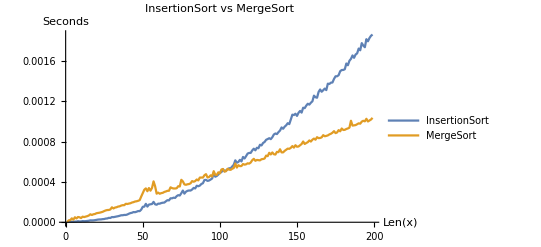

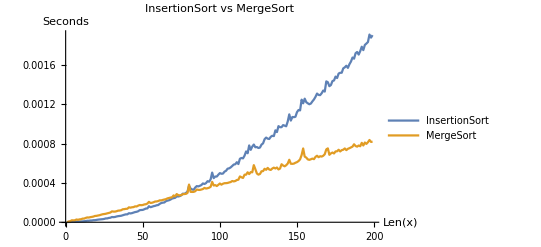

```mathematica
MergesortTimeData= ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/mergeData.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
InsertionTimeData=ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/insertData.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
ListLinePlot[{InsertionTimeData,MergesortTimeData}, PlotLegends->{"InsertionSort","MergeSort"}, AxesLabel->{HoldForm["Len(x)"],HoldForm["Seconds"]},PlotLabel->HoldForm["InsertionSort vs MergeSort"],LabelStyle->{14,GrayLevel[0]}]
```

```mathematica
data=Table[{i,ScientificForm@InsertionTimeData[[i]],ScientificForm@MergesortTimeData[[i]]}, {i,90,110}];
data2=Prepend[data,{"n","InsertionSort","Mergesort"}]
```

{{n,InsertionSort,Mergesort},{90,4.18837×10^-4,4.66314×10^-4},{91,4.20216×10^-4,4.76898×10^-4},{92,4.0984×10^-4,4.43814×10^-4},{93,4.14039×10^-4,4.48785×10^-4},{94,4.23485×10^-4,4.65383×10^-4},{95,4.34085×10^-4,4.53695×10^-4},{96,4.87659×10^-4,5.06538×10^-4},{97,4.51336×10^-4,4.71357×10^-4},{98,4.59073×10^-4,4.69494×10^-4},{99,4.72991×10^-4,4.95376×10^-4},{100,4.92354×10^-4,4.84251×10^-4},{101,4.96398×10^-4,5.22952×10^-4},{102,5.25212×10^-4,5.28316×10^-4},{103,5.05212×10^-4,5.0213×10^-4},{104,5.13915×10^-4,5.06119×10^-4},{105,5.24486×10^-4,5.30281×10^-4},{106,5.35288×10^-4,5.21656×10^-4},{107,5.34988×10^-4,5.19788×10^-4},{108,5.52923×10^-4,5.30629×10^-4},{109,5.69821×10^-4,5.37503×10^-4},{110,6.13861×10^-4,5.82557×10^-4}}

```mathematica
Grid[data2,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text"]
```

n | InsertionSort | Mergesort
90 | 4.18837×10^-4 | 4.66314×10^-4
91 | 4.20216×10^-4 | 4.76898×10^-4
92 | 4.0984×10^-4 | 4.43814×10^-4
93 | 4.14039×10^-4 | 4.48785×10^-4
94 | 4.23485×10^-4 | 4.65383×10^-4
95 | 4.34085×10^-4 | 4.53695×10^-4
96 | 4.87659×10^-4 | 5.06538×10^-4
97 | 4.51336×10^-4 | 4.71357×10^-4
98 | 4.59073×10^-4 | 4.69494×10^-4
99 | 4.72991×10^-4 | 4.95376×10^-4
100 | 4.92354×10^-4 | 4.84251×10^-4
101 | 4.96398×10^-4 | 5.22952×10^-4
102 | 5.25212×10^-4 | 5.28316×10^-4
103 | 5.05212×10^-4 | 5.0213×10^-4
104 | 5.13915×10^-4 | 5.06119×10^-4
105 | 5.24486×10^-4 | 5.30281×10^-4
106 | 5.35288×10^-4 | 5.21656×10^-4
107 | 5.34988×10^-4 | 5.19788×10^-4
108 | 5.52923×10^-4 | 5.30629×10^-4
109 | 5.69821×10^-4 | 5.37503×10^-4
110 | 6.13861×10^-4 | 5.82557×10^-4

```mathematica
Insert[%65,{Background->{None,{GrayLevel[0.7],{White}}},Dividers->{Black,{2->Black}},Frame->True,Spacings->{2,{2,{0.7},2}}},2]
```

n | InsertionSort | Mergesort
90 | 4.18837×10^-4 | 4.66314×10^-4
91 | 4.20216×10^-4 | 4.76898×10^-4
92 | 4.0984×10^-4 | 4.43814×10^-4
93 | 4.14039×10^-4 | 4.48785×10^-4
94 | 4.23485×10^-4 | 4.65383×10^-4
95 | 4.34085×10^-4 | 4.53695×10^-4
96 | 4.87659×10^-4 | 5.06538×10^-4
97 | 4.51336×10^-4 | 4.71357×10^-4
98 | 4.59073×10^-4 | 4.69494×10^-4
99 | 4.72991×10^-4 | 4.95376×10^-4
100 | 4.92354×10^-4 | 4.84251×10^-4
101 | 4.96398×10^-4 | 5.22952×10^-4
102 | 5.25212×10^-4 | 5.28316×10^-4
103 | 5.05212×10^-4 | 5.0213×10^-4
104 | 5.13915×10^-4 | 5.06119×10^-4
105 | 5.24486×10^-4 | 5.30281×10^-4
106 | 5.35288×10^-4 | 5.21656×10^-4
107 | 5.34988×10^-4 | 5.19788×10^-4
108 | 5.52923×10^-4 | 5.30629×10^-4
109 | 5.69821×10^-4 | 5.37503×10^-4
110 | 6.13861×10^-4 | 5.82557×10^-4

```mathematica
TableForm[%58]
```

90 | 4.18837×10^-4 | 4.66314×10^-4
91 | 4.20216×10^-4 | 4.76898×10^-4
92 | 4.0984×10^-4 | 4.43814×10^-4
93 | 4.14039×10^-4 | 4.48785×10^-4
94 | 4.23485×10^-4 | 4.65383×10^-4
95 | 4.34085×10^-4 | 4.53695×10^-4
96 | 4.87659×10^-4 | 5.06538×10^-4
97 | 4.51336×10^-4 | 4.71357×10^-4
98 | 4.59073×10^-4 | 4.69494×10^-4
99 | 4.72991×10^-4 | 4.95376×10^-4
100 | 4.92354×10^-4 | 4.84251×10^-4
101 | 4.96398×10^-4 | 5.22952×10^-4
102 | 5.25212×10^-4 | 5.28316×10^-4
103 | 5.05212×10^-4 | 5.0213×10^-4
104 | 5.13915×10^-4 | 5.06119×10^-4
105 | 5.24486×10^-4 | 5.30281×10^-4
106 | 5.35288×10^-4 | 5.21656×10^-4
107 | 5.34988×10^-4 | 5.19788×10^-4
108 | 5.52923×10^-4 | 5.30629×10^-4
109 | 5.69821×10^-4 | 5.37503×10^-4
110 | 6.13861×10^-4 | 5.82557×10^-4

```mathematica
TableForm[%56]
```

90 | 0.000418837 | 0.000466314
91 | 0.000420216 | 0.000476898
92 | 0.00040984 | 0.000443814
93 | 0.000414039 | 0.000448785
94 | 0.000423485 | 0.000465383
95 | 0.000434085 | 0.000453695
96 | 0.000487659 | 0.000506538
97 | 0.000451336 | 0.000471357
98 | 0.000459073 | 0.000469494
99 | 0.000472991 | 0.000495376
100 | 0.000492354 | 0.000484251
101 | 0.000496398 | 0.000522952
102 | 0.000525212 | 0.000528316
103 | 0.000505212 | 0.00050213
104 | 0.000513915 | 0.000506119
105 | 0.000524486 | 0.000530281
106 | 0.000535288 | 0.000521656
107 | 0.000534988 | 0.000519788
108 | 0.000552923 | 0.000530629
109 | 0.000569821 | 0.000537503
110 | 0.000613861 | 0.000582557

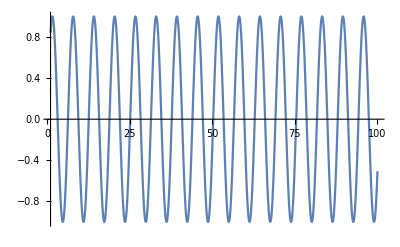

```mathematica
Plot[Sin[x],{x,1,100}]
```

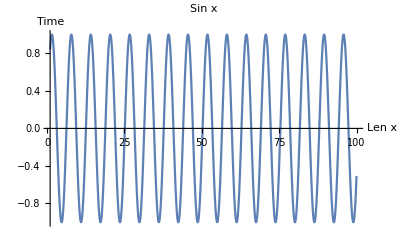

```mathematica
Show[%29,AxesLabel->{HoldForm[Len x],HoldForm[Time]},PlotLabel->HoldForm[Sin x],LabelStyle->{14,GrayLevel[0]}]
```

```mathematica
ListPlot[{Labeled[Sqrt[Range[40]],"sqrt"],Labeled[Log[Range[40,80]],"log"]}]
```

```mathematica
List
```

```mathematica
stringInsertionData ="[2.172216773033142e-06,
 2.386991400271654e-06,
 3.2550073228776454e-06,
 3.548804670572281e-06,
 4.1808118112385275e-06,
 4.62699681520462e-06,
 8.941406849771739e-06,
 1.283758319914341e-05,
 1.4753593131899833e-05,
 1.6183615662157537e-05,
 1.687400508671999e-05,
 1.2944790069013833e-05,
 2.3064203560352325e-05,
 2.8045789804309607e-05,
 1.5660817734897136e-05,
 1.9559613429009913e-05,
 2.6135786902159454e-05,
 2.7300813235342504e-05,
 3.330018371343613e-05,
 3.7305185105651614e-05,
 3.9484212175011633e-05,
 3.218399360775948e-05,
 4.930839641019702e-05,
 3.098699962720275e-05,
 4.203540738672018e-05,
 4.062120569869876e-05,
 9.477022103965282e-05,
 6.0134800150990486e-05,
 6.002722075209022e-05,
 6.693840259686112e-05,
 7.130758604034781e-05,
 5.552339134737849e-05,
 5.608939100056887e-05,
 6.725199054926633e-05,
 6.456279661506414e-05,
 0.00014801417710259558,
 8.085800800472498e-05,
 7.020081393420697e-05,
 0.00010415480937808752,
 8.902701083570718e-05,
 8.749800035730004e-05,
 0.00011625918559730053,
 9.20083955861628e-05,
 9.766798466444015e-05,
 0.00010266458848491311,
 0.00010486918035894633,
 0.00010875760344788432,
 0.00011027560103684663,
 0.00014365740353241562,
 0.00014143720036372543,
 0.0001506783883087337,
 0.00014677800936624408,
 0.00013729239581152796,
 0.0001453725853934884,
 0.0001538469921797514,
 0.00015304078115150333,
 0.00016510660061612724,
 0.00017364181112498046,
 0.00017418900970369577,
 0.00019895300501957536,
 0.00018478779820725323,
 0.00018685780232772232,
 0.00019559439970180393,
 0.00020875001791864634,
 0.0002036397811025381,
 0.0002130356035195291,
 0.00022412720136344433,
 0.0002540847985073924,
 0.000230851408559829,
 0.00024145559873431922,
 0.00024789340095594526,
 0.0002477264148183167,
 0.0002599033992737532,
 0.00025950800627470014,
 0.00029678361024707554,
 0.00029879059875383975,
 0.00028574998723343017,
 0.000295042188372463,
 0.0003072162158787251,
 0.0003250407986342907,
 0.00032063699327409265,
 0.00032160398550331595,
 0.00039247978711500766,
 0.00035699339350685476,
 0.0003622851800173521,
 0.0003776372177526355,
 0.0003636387875303626,
 0.0004032922093756497,
 0.0004039047984406352,
 0.0003570114145986736,
 0.0004247075994499028,
 0.000432335794903338,
 0.00039608380757272243,
 0.0004027353948913515,
 0.0004379549878649414,
 0.00045321702491492034,
 0.00045918121468275787,
 0.0004721066099591553,
 0.0004438084084540606]";
```

```mathematica
5e-4
```

-4+5 e